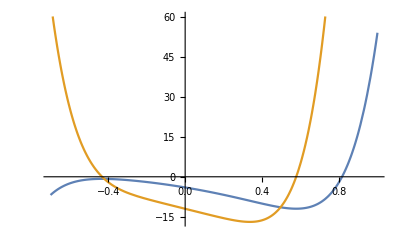

```mathematica
f[x_]:=x^6+6 x^5+12 x^4 6 x^3-9 x^2-12x-4
Plot[{f[x],f'[x]},{x,-0.7,1}, AxesOrigin->{0,0}]
```

```mathematica
f'[1]
```

```mathematica
510
```

```mathematica
l=1/510
```

```mathematica
g[x_]:=x-(x^6+6 x^5+12 x^4 6 x^3-9 x^2-12x-4)/510
x0=0.7; i=1;e=0.00001;x =0;t=10;
For[i, Abs[t-x]≥e,i++, x=g[x0];Print [i," ",x ];t=x0;x0=x]
```

```mathematica
29" "0.8157852743372004
```

```mathematica
22" "0.8155692299146652
```

```mathematica
15" "0.8136499283498294
```